Vaja 3.12.2019: ROM
Vaja s podatki. Shranemo podatke iz excella in notebook ter vse shranimo v isto mapico. Preverimo kje smo s prvima dvema funkcijama. Želimo nastaviti (SetDirectory) tu kjer smo, ker tu imamo mape. Zato samo prekopiramo našo pot (NotebookDirectory).

```mathematica
Directory[]
```

\\Spin\BerdnikA16$\_System\MyDocuments

```mathematica
NotebookDirectory[]
```

U:\PRAKTIČNA MATEMATIKA\ROM - računalniška orodja v matematiki\Vaje 7\

```mathematica
SetDirectory[NotebookDirectory[]]
```

U:\PRAKTIČNA MATEMATIKA\ROM - računalniška orodja v matematiki\Vaje 7

Tako vstavimo excell, mora biti v “ “ dvojnih oklepajih. Kličemo First, da dobimo prvi element iz večjega zunanjega seznama.

```mathematica
podatki = Import["rezultati.xlsx"] // First
```

{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
podatki // TableForm
```

Priimek | Ime | Skupina | Točke
Furlan | Luka | A | 93.
Karakaš | Alenka | A | 94.
Kočar | Petra | B | 44.
Kofol | Andraž | C | 34.
Kumar | Barbara | B | 67.
Logar | Mateja | A | 42.
Pance | Martin | B | 64.
Pleterski | Vesna | C | 30.
Trček | Valerija | B | 70.
Virant | Primož | C | 58.
Vesel | Polona | C | 66.
Žveglič | Katarina | A | 46.
Cvelbar | Janja | B | 39.
Furlan | Aleš | B | 36.
Iskra | Sabina | A | 77.
Jerman | Katja | B | 100.
Karničar | Jaka | C | 26.
Korošec | Kristina | B | 86.
Kržišnik | Grega | B | 90.
Obrenović | Tatjana | C | 44.
Puncer | Primož | A | 57.
Ribnikar | Matjaž | A | 43.
Štemberger | Igor | B | 85.
Šubašič | Matej | C | 76.
Tekavčič | Aleksander | A | 34.
Tratnik | Mojca | B | 79.
Smrekar | Andreja | A | 38.
Bezek | Tomaž | B | 38.

```mathematica
Imena[p_]:=First[p]
```

```mathematica
Imena[podatki]
```

{Priimek,Ime,Skupina,Točke}

Da vzame vse ostalo razen prve vrstice - dejanski podatki

```mathematica
Podatki[p_]:=Rest[p]
```

```mathematica
Podatki[podatki]
```

{{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
Podatki[podatki]//TableForm
```

Furlan | Luka | A | 93.
Karakaš | Alenka | A | 94.
Kočar | Petra | B | 44.
Kofol | Andraž | C | 34.
Kumar | Barbara | B | 67.
Logar | Mateja | A | 42.
Pance | Martin | B | 64.
Pleterski | Vesna | C | 30.
Trček | Valerija | B | 70.
Virant | Primož | C | 58.
Vesel | Polona | C | 66.
Žveglič | Katarina | A | 46.
Cvelbar | Janja | B | 39.
Furlan | Aleš | B | 36.
Iskra | Sabina | A | 77.
Jerman | Katja | B | 100.
Karničar | Jaka | C | 26.
Korošec | Kristina | B | 86.
Kržišnik | Grega | B | 90.
Obrenović | Tatjana | C | 44.
Puncer | Primož | A | 57.
Ribnikar | Matjaž | A | 43.
Štemberger | Igor | B | 85.
Šubašič | Matej | C | 76.
Tekavčič | Aleksander | A | 34.
Tratnik | Mojca | B | 79.
Smrekar | Andreja | A | 38.
Bezek | Tomaž | B | 38.

Indeks stolpca:

```mathematica
Position[Imena[podatki], "ime"]
```

{}

{}

Zaradi sintaktične napake prazna množica.

```mathematica
Position[Imena[podatki], "Ime"]
```

{{2}}

Pomeni da so v drugem stolpcu shranjena imena.

```mathematica
Position[{1,{1,2}},1]
```

{{1},{2,1}}

Pomeni da je 1 na prvem mestu celotnega seznama in na prvem mestu drugega elementa -> {2,1}

```mathematica
IndeksStoplca[podatki_, stolpec_]:=Module[{},
mesto=Position[Imena[podatki],stolpec];
If[Length[mesto]==0, Null, mesto[[1,1]]]
]
```

Če je prazna množica, kot pri ‘ime’ vrne nič, sicer pa odgovori.

```mathematica
IndeksStoplca[podatki, "ime"]
```

```mathematica
IndeksStoplca[podatki, "Ime"]
```

2

```mathematica
podatki
```

{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

Transponiramo, da dobimo podatke drugače obrnjenje, saj bi zdaj mogli za piimke jemati vse druge elemente podseznamov.

```mathematica
kateri=IndeksStolpca[podatki, "Ime"];
Transpose[Podatki[podatki]][[kateri]]
```

Part::pkspec1: The expression IndeksStolpca[{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}},Ime] cannot be used as a part specification.

{{Furlan,Karakaš,Kočar,Kofol,Kumar,Logar,Pance,Pleterski,Trček,Virant,Vesel,Žveglič,Cvelbar,Furlan,Iskra,Jerman,Karničar,Korošec,Kržišnik,Obrenović,Puncer,Ribnikar,Štemberger,Šubašič,Tekavčič,Tratnik,Smrekar,Bezek},{Luka,Alenka,Petra,Andraž,Barbara,Mateja,Martin,Vesna,Valerija,Primož,Polona,Katarina,Janja,Aleš,Sabina,Katja,Jaka,Kristina,Grega,Tatjana,Primož,Matjaž,Igor,Matej,Aleksander,Mojca,Andreja,Tomaž},{A,A,B,C,B,A,B,C,B,C,C,A,B,B,A,B,C,B,B,C,A,A,B,C,A,B,A,B},{93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}}⟦IndeksStolpca[{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}},Ime]⟧

```mathematica
Stolpec[podatki_, stolpec_]:=Module[{kateri}, 
kateri = IndeksStoplca[podatki, stolpec];
Transpose[Podatki[podatki]][[kateri]]
]
```

```mathematica
Stolpec[podatki, "Točke"]
```

{93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}

Izračunajmo povprečje točk, funkcija Mean

```mathematica
Mean[{1,2,3,4}]
```

5/2

```mathematica
Mean[Stolpec[podatki, "Točke"]]
```

59.1429

```mathematica
PovprečjeTočk[podatki_]:=Mean[Stolpec[podatki, "Točke"]]
```

```mathematica
PovprečjeTočk[podatki]
```

59.1429

Želimo zapisati le število skupin, ne pa da se ponavljajo, samo zanimajo nas katere so. To storimo z funkcijo Union

```mathematica
RazlicneVrednosti[podatki_, stolpec_]:=Union[Stolpec[podatki, stolpec]]
```

```mathematica
RazlicneVrednosti[podatki, "Skupina"]
```

{A,B,C}

Želimo dobiti še i-to vrstico

```mathematica
Vrstica[podatki_, i_]:=Podatki[podatki][[i]]
```

```mathematica
OcenaZaMeje[{za6_, za7_, za8_,za9_,za10_},tocke_]:=Module[{},
If[tocke≥za10, Return[10]];
If[tocke≥za9, Return[9]];
If[tocke≥za8, Return[8]];
If[tocke≥za7, Return[7]];
If[tocke≥za6, Return[6]];
0
]
```

```mathematica
OcenaZaMeje[55]
```

```mathematica
OcenaZaMeje[55]
```

```mathematica
meje={50,60,70,80,90}
```

{50,60,70,80,90}

```mathematica
OcenaZaMeje[meje, 55]
```

6

```mathematica
OcenaZaMeje[meje,45]
```

0

```mathematica
tocke=Stolpec[podatki, "Točke"];
meje={50,60,70,80,90};
izracunajOceno[tocke_]:=OcenaZaMeje[meje, tocke]
ocene = Map[izracunajOceno, tocke]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
ocene
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
ClearAll[DodajStolpec]
```

```mathematica
DodajStolpec[podatki_, ime_, podStolpec_]:=Module[{imena},
imena=Append[Imena[podatki], ime];
noviPodatki = Transpose[Append[Transpose[Podatki[podatki]], podStolpec]];
Prepend[noviPodatki, imena]
]
```

```mathematica
podatkiOcene=DodajStolpec[podatki, "Ocene", ocene]
```

{{Priimek,Ime,Skupina,Točke,Ocene},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Kočar,Petra,B,44.,0},{Kofol,Andraž,C,34.,0},{Kumar,Barbara,B,67.,7},{Logar,Mateja,A,42.,0},{Pance,Martin,B,64.,7},{Pleterski,Vesna,C,30.,0},{Trček,Valerija,B,70.,8},{Virant,Primož,C,58.,6},{Vesel,Polona,C,66.,7},{Žveglič,Katarina,A,46.,0},{Cvelbar,Janja,B,39.,0},{Furlan,Aleš,B,36.,0},{Iskra,Sabina,A,77.,8},{Jerman,Katja,B,100.,10},{Karničar,Jaka,C,26.,0},{Korošec,Kristina,B,86.,9},{Kržišnik,Grega,B,90.,10},{Obrenović,Tatjana,C,44.,0},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Štemberger,Igor,B,85.,9},{Šubašič,Matej,C,76.,8},{Tekavčič,Aleksander,A,34.,0},{Tratnik,Mojca,B,79.,8},{Smrekar,Andreja,A,38.,0},{Bezek,Tomaž,B,38.,0}}

```mathematica
podatkiOcene//TableForm
```

Priimek | Ime | Skupina | Točke | Ocene
Furlan | Luka | A | 93. | 10
Karakaš | Alenka | A | 94. | 10
Kočar | Petra | B | 44. | 0
Kofol | Andraž | C | 34. | 0
Kumar | Barbara | B | 67. | 7
Logar | Mateja | A | 42. | 0
Pance | Martin | B | 64. | 7
Pleterski | Vesna | C | 30. | 0
Trček | Valerija | B | 70. | 8
Virant | Primož | C | 58. | 6
Vesel | Polona | C | 66. | 7
Žveglič | Katarina | A | 46. | 0
Cvelbar | Janja | B | 39. | 0
Furlan | Aleš | B | 36. | 0
Iskra | Sabina | A | 77. | 8
Jerman | Katja | B | 100. | 10
Karničar | Jaka | C | 26. | 0
Korošec | Kristina | B | 86. | 9
Kržišnik | Grega | B | 90. | 10
Obrenović | Tatjana | C | 44. | 0
Puncer | Primož | A | 57. | 6
Ribnikar | Matjaž | A | 43. | 0
Štemberger | Igor | B | 85. | 9
Šubašič | Matej | C | 76. | 8
Tekavčič | Aleksander | A | 34. | 0
Tratnik | Mojca | B | 79. | 8
Smrekar | Andreja | A | 38. | 0
Bezek | Tomaž | B | 38. | 0

To je splošna funckija ne glede na to kakšen stolpec bomo vstavili.

Želimo nazaj izvosti v excell. Uporabimo funckijo Export. Preveriti moramo ali smo v pravi mapci

```mathematica
novi = DodajStolpec[podatki, "Ocene", ocene]
```

{{Priimek,Ime,Skupina,Točke,Ocene},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Kočar,Petra,B,44.,0},{Kofol,Andraž,C,34.,0},{Kumar,Barbara,B,67.,7},{Logar,Mateja,A,42.,0},{Pance,Martin,B,64.,7},{Pleterski,Vesna,C,30.,0},{Trček,Valerija,B,70.,8},{Virant,Primož,C,58.,6},{Vesel,Polona,C,66.,7},{Žveglič,Katarina,A,46.,0},{Cvelbar,Janja,B,39.,0},{Furlan,Aleš,B,36.,0},{Iskra,Sabina,A,77.,8},{Jerman,Katja,B,100.,10},{Karničar,Jaka,C,26.,0},{Korošec,Kristina,B,86.,9},{Kržišnik,Grega,B,90.,10},{Obrenović,Tatjana,C,44.,0},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Štemberger,Igor,B,85.,9},{Šubašič,Matej,C,76.,8},{Tekavčič,Aleksander,A,34.,0},{Tratnik,Mojca,B,79.,8},{Smrekar,Andreja,A,38.,0},{Bezek,Tomaž,B,38.,0}}

```mathematica
?Export
```

```mathematica
Directory[]
```

\\Spin\BerdnikA16$\_System\MyDocuments

```mathematica
NotebookDirectory[]
```

U:\PRAKTIČNA MATEMATIKA\ROM - računalniška orodja v matematiki\Vaje 7\

```mathematica
Export["ocene.xlsx", novi]
```

ocene.xlsx

Zanima nas kaj dela funkcija BinCounts

```mathematica
ocene
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
porazdelitevOcen=Drop[Rest[BinCounts[ocene]],{2,6}]
```

{13,2,3,4,2,4}

13 negativnih...4 desetke (ocene)
Radi bi narisali stolpični diagram

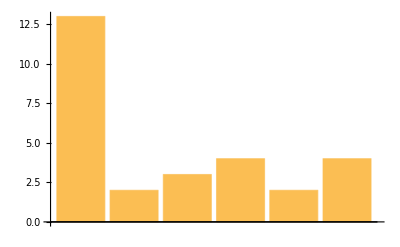

```mathematica
BarChart[porazdelitevOcen]
```

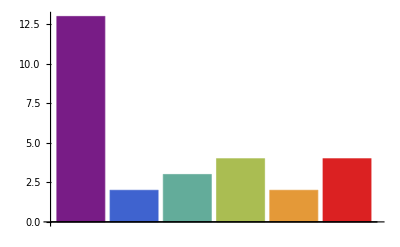

```mathematica
BarChart[porazdelitevOcen, ChartStyle->"Rainbow"]
```

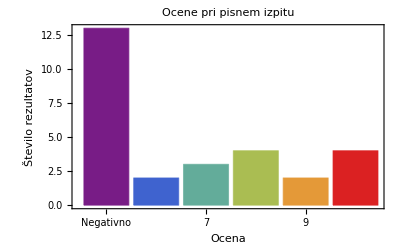

```mathematica
BarChart[porazdelitevOcen, ChartStyle->"Rainbow", 
PlotLabel-> "Ocene pri pisnem izpitu",
ChartLabels->{"Negativno", 6,7,8,9,10},
Frame->True,
FrameLabel->{"Ocena","Število rezultatov"}
]
```

```mathematica
napisi = {"Negativno", 6,7,8,9,10}
```

{Negativno,6,7,8,9,10}

```mathematica
BarChart[porazdelitevOcen, ChartStyle->"Rainbow", 
PlotLabel-> "Ocene pri pisnem izpitu",
ChartLabels->napisi,
Frame->True,
FrameLabel->{"Ocena","Število rezultatov"}
]
```

-Graphics-

Radi bi narisali še tortni (pitni) diagram.

```mathematica
PieChart3D[porazdelitevOcen]
```

-Graphics3D-

Ker je 3D ga lahko še ročno vrtimo z miško.

Zanima nas število vseh ocen:

```mathematica
Length[ocene]
```

28

Zanimajo nas deleži ocen glede na vse.

```mathematica
N[porazdelitevOcen/Length[ocene]*100, 2]
```

{46.,7.1,11.,14.,7.1,14.}

```mathematica
?DecimalForm
```

Želimo uporabiti to funkcijo namesto N

```mathematica
DecimalForm[N[porazdelitevOcen/Length[ocene]*100],{3,1}]
```

{46.4,7.1,10.7,14.3,7.1,14.3}

Radi bi to uporabili in zapisali procente ocen. Moramo ‘združiti’ spodnja dva seznama. Sta iste dolžine.

```mathematica
procenti = DecimalForm[N[porazdelitevOcen/Length[ocene]*100],{3,1}]
```

{46.4,7.1,10.7,14.3,7.1,14.3}

```mathematica
napisi
```

{Negativno,6,7,8,9,10}

Želimo uporabiti StringJoin a ni dovolj pametna funkcija. Vsi elementi morajo biti string.

```mathematica
StringJoin[1,3]
```

StringJoin::string: String expected at position 1 in 1<>3.

StringJoin::string: String expected at position 2 in 1<>3.

1<>3

```mathematica
StringJoin["1",3]
```

StringJoin::string: String expected at position 2 in 1<>3.

1<>3

```mathematica
StringJoin["1","3"]
```

13

Uporabimo šte funkcijo ToString.

```mathematica
?ToString
```

```mathematica
zdruzi[napis_,procent_]:=StringJoin[ToString[napis], " (", ToString[procent], "%)"]
```

```mathematica
zdruzi["Negativno",46.4]
```

Negativno (46.4%)

```mathematica
?MapThread
```

```mathematica
MapThread[zdruzi, {napisi, procenti}]
```

MapThread::mptd: Object {46.4,7.1,10.7,14.3,7.1,14.3} at position {2, 2} in MapThread[zdruzi,{{Negativno,6,7,8,9,10},{46.4,7.1,10.7,14.3,7.1,14.3}}] has only 0 of required 1 dimensions.

MapThread[zdruzi,{{Negativno,6,7,8,9,10},{46.4,7.1,10.7,14.3,7.1,14.3}}]

```mathematica
?zdruzi
```

Problem je DecimalForm. Samo izpiše nam ampak ni prava struktura. Ker kot MatrixForm ali TableForm izpište le pravo obliko. Ne pa tudi poračuna, skrbi le za prikaz. Uporabili bomo drugo funckijo

```mathematica
procenti = DecimalForm[N[porazdelitevOcen/Length[ocene]*100],{3,1}]
```

{46.4,7.1,10.7,14.3,7.1,14.3}

```mathematica
zaokrozi[n_]:=ToString[DecimalForm[n,{3,1}]]
```

```mathematica
procenti=Map[zaokrozi,N[porazdelitevOcen/Length[ocene]*100]]
```

{46.4,7.1,10.7,14.3,7.1,14.3}

Uporabili smo funkcijo Map, ki gre čez vse elemente in sproži funkcijo združi.

```mathematica
zdruzi[napis_,procent_]:=StringJoin[ToString[napis], " (", ToString[procent], "%)"]
```

```mathematica
noviNapisi=MapThread[zdruzi, {napisi, procenti}]
```

{Negativno (46.4%),6 (7.1%),7 (10.7%),8 (14.3%),9 (7.1%),10 (14.3%)}

Zdaj želimo te napise uporabiti na tortnem grafu.

```mathematica
PieChart3D[porazdelitevOcen,ChartLabels->noviNapisi, ChartStyle->"Rainbow"]
```

-Graphics3D-

Napiši funkcijo UstrezaPogoju[podatki_, vrstica_, stolpec_, primerjava_, vrednost_], ki vrne True, če vrstica iz table podatki ustreza pogoju, da za vrednost v v stolpcu stolpec velja primerjava[v, vrednost] je True. 
Primer:
v1 = Vrstica[podatkiOcene, 2] {“Karakaš”, “Alenka”, “A”, 94., 10}
v2 = Vrstica[podatkiOcene, 3] {“Kočar”, “Petra”, “B”, 44., 0}
UstrezaPogoju[podatkiOcene, v1, “Ocena”, Equal, 10] True
UstrezaPogoju[podatkiOcene, v2, “Ocena”, Equal, 10] False

```mathematica
FullForm[a==b]
```

Equal[a,b]

```mathematica
podatki
```

{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
UstrezaPogoju[podatki_, vrstica_, stolpec_, primerjava_, vrednost_]:=Module[{indeks,element},
indeks=IndeksStoplca[podatki, stolpec];
element=vrstica[[indeks]];
primerjava[element, vrednost]
]
```

```mathematica
v1 =Vrstica[podatkiOcene, 2]
v2=Vrstica[podatkiOcene,3]
```

{Karakaš,Alenka,A,94.,10}

{Kočar,Petra,B,44.,0}

```mathematica
v1
```

{Karakaš,Alenka,A,94.,10}

```mathematica
UstrezaPogoju[podatkiOcene,v1,"Ocena", Equal, 10]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

{Karakaš,Alenka,A,94.,10}⟦Null⟧==10

```mathematica
UstrezaPogoju[podatkiOcene, v2, "Ocena", Equal, 10]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

{Kočar,Petra,B,44.,0}⟦Null⟧==10

```mathematica
IzberiVrstice[podatki_, stolpec_, primerjava_, vrednost_]:=Module[{pod, izberiVrstico},
pod=Podatki[podatki];
izberiVrstico[v_]:=UstrezaPogoju[podatki, v, stolpec, primerjava, vrednost];
Select[pod, izberiVrstico]
]
```

```mathematica
IzberiVrstice[podatkiOcene,"Ocena", GreaterEqual, 9]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{}

```mathematica
podatkiOcene
```

podatkiOcene